```mathematica
Quit[]
```

```mathematica
SetDirectory["~/Documents/Univ/chi-q_dist/num"]
```

/Users/yuichirotada/Documents/Univ/chi-q_dist/num

```mathematica
νth=8;
KK=3.3;
β=0.36;
γ=0.85;
```

```mathematica
δbH=0.768;
νbth=2/5 νth;
σH=δbH/νbth
```

0.24

```mathematica
Ph[h_]=563 h^2 Exp[−12h+2.5 h^1.5+8−3.2(1500+h^16)^(1/8)];
Cν[ν_]=1.56 10^-3 Sqrt[1-γ^2] KK^(-1/3)σH^(-β/3)(ν-νth)^(-1/3)((2/5 ν)/8)^-2;
```

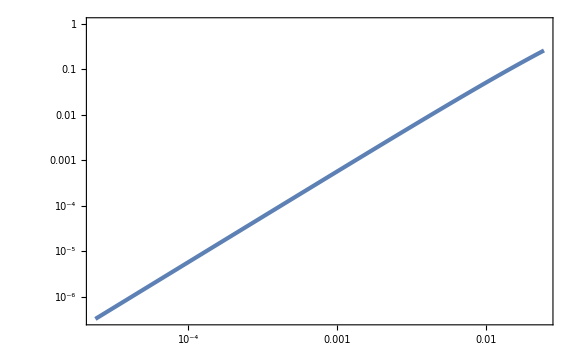

```mathematica
LogLogPlot[Ph[h],{h,0,Cν[8.000000000001]^-1}]
```

```mathematica
Na[ν_]:=NIntegrate[Ph[h],{h,0,Cν[ν]^-1}]
```

```mathematica
NaList=Table[{νth+10^dlogν,Na[νth+10^dlogν]},{dlogν,-10,1,1/100}];
```

```mathematica
Naint[ν_]=Interpolation[NaList][ν];
```

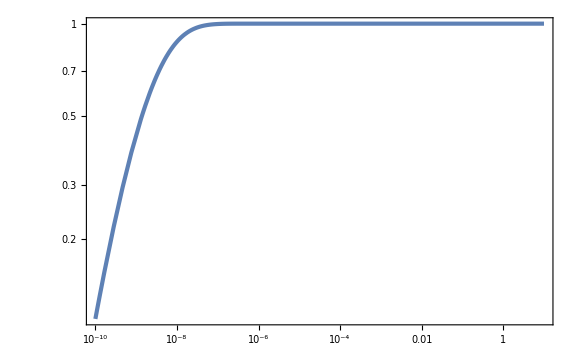

```mathematica
LogLogPlot[Naint[νth+δν],{δν,10^-10,10},PlotRange->Full]
```

```mathematica
Pa[a_,ν_]=(Cν[ν]^-1 Ph[Cν[ν]^-1 a])/Naint[ν];
```

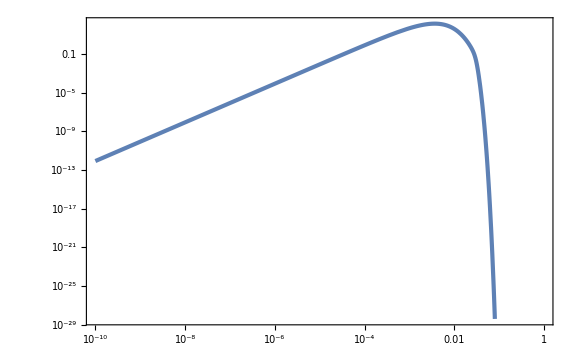

```mathematica
LogLogPlot[Pa[a,νth+10^-2],{a,10^-10,1}]
```

```mathematica
NIntegrate[Pa[a,νth+10^1],{a,0,1}]
```

1.

```mathematica
LL[a1_,a2_,χ_,q_]=Min[1,((1+q)χ+q a2)/a1]-Max[-1,((1+q)χ-q a2)/a1];
Pν[ν_]=Sqrt[2/π] Erfc[νth/Sqrt[2]]^-1 Exp[-ν^2/2];
ν2[ν1_,q_]=q^(1/β)(ν1-νth)+νth;
```

```mathematica
ν2[νth+10,0]
```

8.

```mathematica
Clear[Pintegrand]
```

```mathematica
Pintegrand[χ_,q_,log10a1_,log10a2_,log10δν1_]:=LL[10^log10a1,10^log10a2,χ,q] Log[10]^3 10^(log10a1+2log10δν1)Pa[10^log10a1,νth+10^log10δν1]Pν[νth+10^log10δν1]Pa[10^log10a2,ν2[νth+10^log10δν1,q]]Pν[ν2[νth+10^log10δν1,q]]/;LL[10^log10a1,10^log10a2,χ,q]>0
Pintegrand[χ_,q_,log10a1_,log10a2_,log10δν1_]:=0/;!(LL[10^log10a1,10^log10a2,χ,q]>0)
```

```mathematica
Pintegrand[0,1,-5,-5,-5]
```

1.12002×10^-22

```mathematica
Pχq[χ_,q_]:=NIntegrate[Pintegrand[χ,q,log10a1,log10a2,log10δν1],{log10a1,-5,0},{log10a2,-5,0},{log10δν1,-5,1}]
```

```mathematica
Pχq[0,1]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 2000 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained 182.727 and 0.00218714 for the integral and error estimates.

182.727

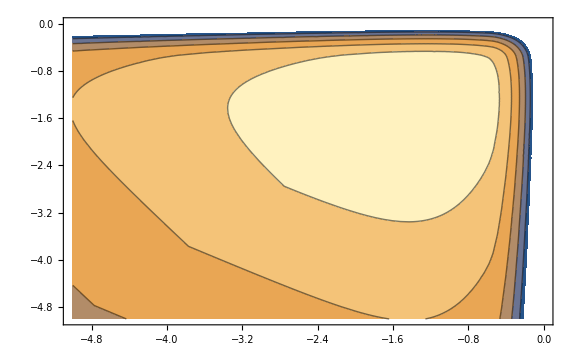

```mathematica
ContourPlot[Log10[Pintegrand[0,1,log10a1,log10a2,-5]],{log10a1,-5,0},{log10a2,-5,0}]
```

```mathematica
Pχ0List=Table[{i/10,Pχq[0,i/10]//Quiet},{i,1,10}];//AbsoluteTiming
```

{333.723,Null}

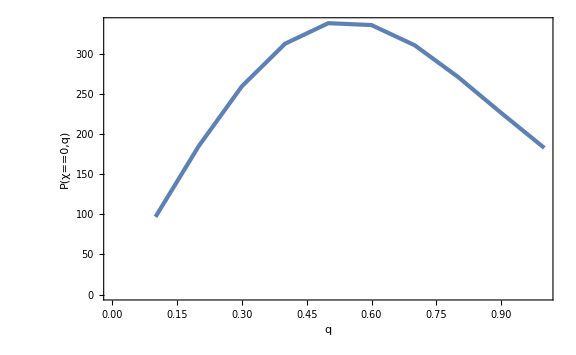

```mathematica
ListPlot[Pχ0List,FrameLabel->{q,P[χ==0,q]}]
```